We describe changes in thoracic and surface temperature as a function of environmental temperature during warm-up (passive or active heating). I define environmental temperature as the real temperature and thus include air temperature, humidity and wind speed. First, the change in thoracic temperature is based on conduction from surface to temperature. We assume that there is no heat  generated from metabolism and respiration or they cancel each other. Thus, change in body temperature is a result of exchange of energy between the body and the surface. Here, surface means anything between the thorax and the environment thus z_ = z_th + z_s where z_th(z_s)is  thoracic (surface) mass.

Now, we describe changes in energy in the thorax as results of endogeneous heat production as thorax shivers. We have
dQ_th/dt= z_th e f[T_th] + A_th K_sth(T_s- T_th)
where e is the energy generated per gram of muscle constraction, f is the increase in frequency of muscle contraction as thoracic temperature T_th increases. A_th is the total (inner) surface-area of the thorax and K_sb is the conduction coefficient between the body and the surface. 

The flux of energy in the surface is   
dQ_s/dt =  - A_th K_sth(T_s-T_th) + A_s[K_es(T_e-T_s) - K_v(T_s-T_e)   - σ ε T_s^4  +Q_abs]
where A_s is the total (outter) surface of the body, K_es is the conduction coefficient between the environment and the surface. K_v =   1.4 × 0.135 √(u/d) × c_p is the convetion coefficient, c_pis the specific heat of air (29.3 J mol^-1 K^-1), u is the wind speed and d the characteristic dimenion of the animal. d can be either V^(1/3) (V = volume), or 0.81 w  (w = diameter of the sphere) (p107 Campbell and Norman), the factor 1.4 corrects for turbulence.  σ = 5.67 × 10^-8 J  s^-1 m^-2 K^-4 is the Stefan-Boltzmann constant and ε = 0.975  is the emissivity of gray body. Q_abs the total radiation from the envirnomnent, it is the sum of direct irradiance on surface perpendicular to the beam, diffuse sky irradiance, total irradiance from the horizontal surface, and reflected radiation from the ground. Each irradiance does depend on other factors such as view factors of the body, elevation and so on. However, since each component does not depend on surface area, we vary directly Q_abs rather than making its components realistic. 

Finally, the change in body temperature during heating is 
dT_th/dt= =  1/(s_th z_th) dQ_th/dt=1/(s_th z_th) ( z_th e f[T_th]  + A_th K_sth(T_s- T_th) )
dT_s/dt =1/(s_s z_s) dQ_s/dt= 1/(s_s z_s) (- A_thK_sth(T_s-T_th) + A_s [- ρ K_v(T_s-T_e)   - σ ε T_s^4   + σ ε T_e^4  +Q_abs]). 
If the individual is not capable of endogeneous heat production, f is equal to zero. s_th and s_s are the specific heat capacity of the thorax and the remaning body part, respectively.

We can solve this numerically to find for a given body size if minimal temperature for activity is reached and how long it takes to warm-up.

```mathematica
(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 10^(6);(* g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 *);
(*2.092 10 ^(-12)*)  (*5 10^(-7) cal/s C mm2 = 4.184 *5 10^(-7) 10^(-6) W/C m2 *)

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s *);
(*, Conversion: 1 cal = 4.184 J, 1m2 = (1000 mm)^2 = 10^6 mm2 thus 1 mm2 = 10^(-6) m2*)

aw = 0.25; (*something per second*)
f[T_]:= aw T;

(*Start from radius calculating it is easier *)
rad[z_]:= (3. z/(2 π δ))^(1/3);
As[z_]:= 3. π rad[z]^2 (* m2*); (* Total surface area*)
Ath[z_]:= 2. π(rad[z])^2;  (*Thoracic surface area, circle surface =  π r^2, sphere surface = 4 π r^2 *)
```

```mathematica
(*Solving dTth/dt and and dTs/dt*)
ThoraxT[z_,J_,ϕ_,t0_,endo_]:=Module[{result= {},solrad,temperature,zth ,zs, Athv, Asv, r = rad[z],Kvv,fact,oldTth,oldTs,newTth,newTs, a1, b1, T0,dt ,ε= 0.95,const =0.5,fS,fT,temp,invdt},
If[endo==True, fact = 0.1, fact =0];

a1 = 4; b1 =0.00825/2;T0 =25;
(*Calculate solar radiation, per minute increment*)
solrad =Table[1000SolarRadiation[J,t,ϕ],{t,0,24,1}];
fS=Interpolation[solrad];
(*Caclulate daily temperature,the code works per minute increment*)
temperature = DailyTemperature[J,ϕ,a1,b1,T0];
fT= Interpolation[temperature];

(*mass of thorax and the rest of the body*)
zth = z/2;
zs = z/2;

(*calculate As and Ath*)
Athv = Ath[z];
Asv =As[z];
(*calculate convectivity*)
Kvv= Kv[z];

oldTth = fT[t0];
oldTs= oldTth;

 dt =1; (*This is one second*)
invdt= 3600/dt;(* dt in hours*)
Do[
newTth =oldTth + dt (1./ (s zth)) (fact zth e  f[oldTth] + Athv Ksth (oldTs - oldTth));
(*Print[Athv Ksth (oldTs - oldTth)];*)
newTs= oldTs + dt (1./ (s zs)) (- Athv Ksth (oldTs- oldTth)+Asv(-Kvv 1(oldTs - fT[tt/invdt]) - σ ε (oldTs+273.2)^4 + + σ ε (fT[tt/invdt]+273.2)^4  + const fS[tt/invdt]));
temp = {tt/invdt,newTs,oldTth};
oldTth = newTth;
oldTs= newTs;
If[oldTth>50,Goto[here]];
AppendTo[result,temp];
,{tt,t0*invdt,(t0+1)*invdt,dt(* 24.*invdt*)}];
Label[here];
result]
```

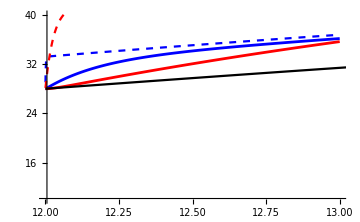

```mathematica
a1 =8; b1 =0.00825;T0 = 25; cT0=ConstantArray[T0,24];th = 2;
t0 =12; ph =30; J = t1; z1 = 0.01;z2 =5;
d1 =ThoraxT[z1,J,ph,t0,False];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z2,J,ph,t0,False];

fig2a =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t0+1},{10,40}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium]
```

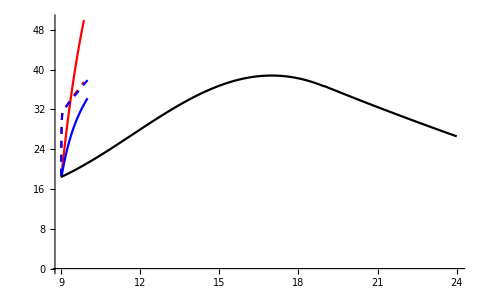

```mathematica
t0 = 9; ph =30; J = t1; z1 = 0.01;z2 =1;
d1 =ThoraxT[z2,J,ph,t0,True];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z2,J,ph,t0,False];

fig2a =ListPlot[{d1[[All,{1,2}]],d1[[All,{1,3}]],d2[[All,{1,2}]],d2[[All,{1,3}]],dT},Joined->True,PlotStyle->{{Dashed,Red},{Red},{Dashed,Blue},{Blue},{Black}},PlotRange->{All,{0,50}}]
```

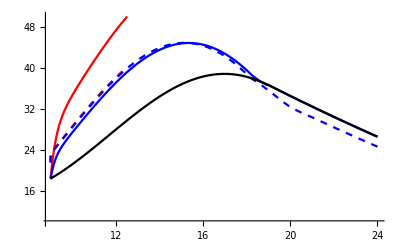

```mathematica
t0 =9; ph =30; J = t1; z1 = 0.1;z2 =1;
d1 =ThoraxT[z1,J,ph,t0,True];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z1,J,ph,t0,False];

fig2b =ListPlot[{d1[[All,{1,2}]],d1[[All,{1,3}]],d2[[All,{1,2}]],d2[[All,{1,3}]],dT},Joined->True,PlotStyle->{{Dashed,Red},{Red},{Dashed,Blue},{Blue},{Black}},PlotRange->{All,{10,50}}]
```

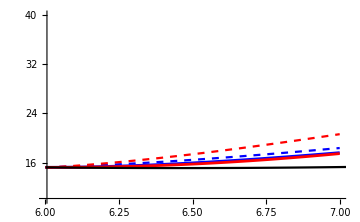

```mathematica
a1 =8; b1 =0.00825;T0 = 25; cT0=ConstantArray[T0,24];th = 2;
t0 =6; ph =30; J = t1; z1 = 0.1;z2 =5;
d1 =ThoraxT[z1,J,ph,t0,False];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z2,J,ph,t0,False];

fig2a =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t0+1},{10,40}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium]
```

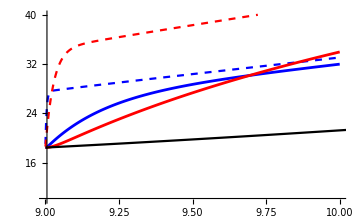

```mathematica
a1 =8; b1 =0.00825;T0 = 25;th = 2;
t0 =9; ph =30; J = t1; z1 = 0.1;z2 =5;
d1 =ThoraxT[z1,J,ph,t0,False];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z2,J,ph,t0,False];

fig2b =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{9,10},{10,40}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium]
```

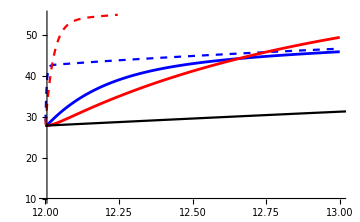

```mathematica
a1 =8; b1 =0.00825;T0 = 25; cT0=ConstantArray[T0,24];th = 2;
t0 =12; ph =30; J = t1; z1 = 0.1;z2 =5;
d1 =ThoraxT[z1,J,ph,t0,False];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z2,J,ph,t0,False];

fig2c =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t0+1},{10,55}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium]
```

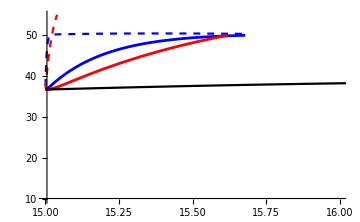

```mathematica
a1 =8; b1 =0.00825;T0 = 25; cT0=ConstantArray[T0,24];th = 2;
t0 =15; ph =30; J = t1; z1 = 0.1;z2 =5;
d1 =ThoraxT[z1,J,ph,t0,False];
d02 = DailyTemperature[J,ph,a1,b1,T0];
ff = Interpolation[DailyTemperature[t1,30,a1/2,b1/2,T0]];
dT = Table[{tt,ff[tt]},{tt,t0,24,1./60}];

d2=ThoraxT[z2,J,ph,t0,False];

fig2d =ListPlot[{d1[[All,{1,3}]],d1[[All,{1,2}]],d2[[All,{1,3}]],d2[[All,{1,2}]],dT},Joined->True,PlotStyle->{{Blue,AbsoluteThickness[th]},{Blue,Dashed},{Red,AbsoluteThickness[th]},{Red,Dashed},{Black}},PlotRange->{{t0,t0+1},{10,55}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium]
```

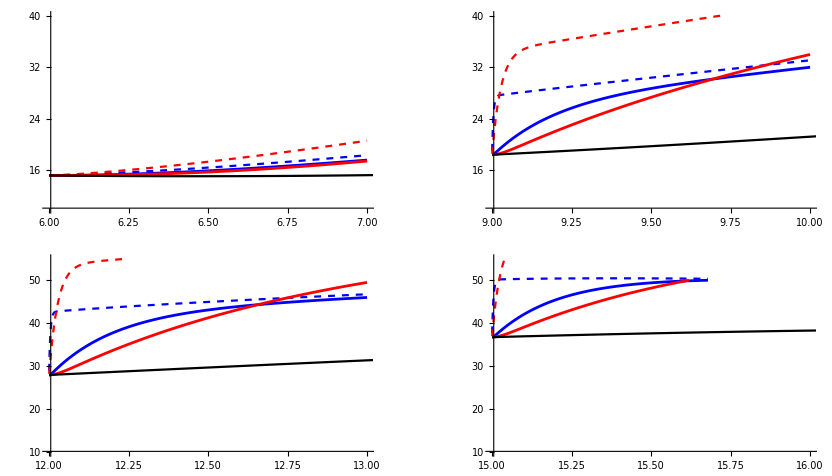

```mathematica
GraphicsGrid[{{Show[fig2a,ImagePadding->{{40,10},{Automatic,Automatic}}],Show[fig2b,ImagePadding->{{40,10},{Automatic,Automatic}}]},{Show[fig2c,ImagePadding->{{40,10},{Automatic,Automatic}}],Show[fig2d,ImagePadding->{{40,10},{Automatic,Automatic}}]}},Spacings->{50,10}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\10 ms\\nb\\warm-up.pdf",%,"PDF"]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\10 ms\nb\warm-up.pdf

```mathematica
(*Calculating Qabs*)
(*
The original formula is Rabs = αs(Fp Sp + Fd Sd + Fr Sr) + αL (Fa La + Fg Lg);

*)
σ=5.67 10^(-8);(*W/m2 K4*)
Qabs[Rad_,ψ_]:= Module[{result,αs},
αs = 
result]
```

```mathematica
(*Calculating Qabs*)
σ=5.67 10^(-8);(*W/m2 K4*)
Qabs[ψ_,Ta_,Tg_]:= Module[{result,Sp0 = 1361,Sp,St,Sr, Sb,Sd,DtoR = π/180, pa = 101.3 (*elevation 0*), m,τ  =0.7, ρs =0.15 (*see table 11.2*), αs = 0.9,αL = 0.965,Fp, Fa = 0.5, Fg = 0.5, Fr= 0.5, Fd = 0.8, La,Lg},
Sp = Sp0 τ^(1/Cos[ψ DtoR]);ss =Sp;
(*effect Sp after taking atmospheric presure at 0 elev and  transmittance*);
Sd = Sp0 0.3 (1- τ^(1/Cos[ψ DtoR])) ;
Sb = Sp Cos[ψ DtoR];
St = Sb +Sd;
Sr = ρs St;
Fp = 0.5 Cos[ψ DtoR];
La= σ (273.2+Ta)^4;
Lg = σ (273.2+Tg)^4;
val = αs (Fp Sp + Fd Sd + Fr Sr);
result = αs (Fp Sp + Fd Sd + Fr Sr) + αL (Fa La + Fg Lg);
result]
```

```mathematica
Qabs[60,0,0]
```

641.354

```mathematica
ss
```

666.89

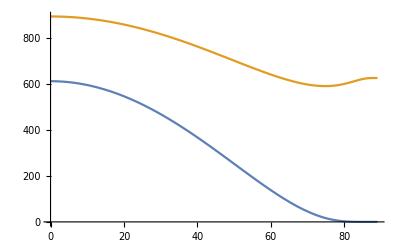

```mathematica
Plot[{1361 * Cos[ps π/180]*0.45^ (1/Cos[ps π/180]),Qabs[ps, 0,0]},{ps,0,89}]
```

```mathematica
σ(273.2+30)^4
```

479.181

```mathematica
1/Cos[85.* π/180]
```

11.4737